# Power

### Author

Eric W. Weisstein
December 3, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/SpecialFunctions/Power.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Power.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

## Plots

#### V5

```mathematica
Show[Plot[Evaluate[Table[x^n,{n,-3,3}]],Evaluate[{x,Sequence@@#}],DisplayFunction->Identity,PlotStyle->{Red,Yellow,Green,Black,Blue,Indigo,Violet},AxesLabel->TraditionalForm/@{x,x^n},PlotRange->{Automatic,{-10,10}}]&/@{{-3,0},{0,3}},DisplayFunction->$DisplayFunction]
```

⁃Graphics⁃

```mathematica
Plot[Evaluate[Table[x^n,{n,0,3,.5}]],{x,0,3},PlotStyle->{Black,Red,Yellow,Green,Blue,Indigo,Violet},AxesLabel->TraditionalForm/@{x,x^n}]
```

⁃Graphics⁃

```mathematica
Plot[Table[x^n,{n,-4,4,.5}]//Evaluate,{x,0.01,2},
AspectRatio->Automatic,Ticks->None,PlotRange->{Automatic,{-.05,2}}]
```

⁃Graphics⁃

#### V6

```mathematica
Needs["Graphics`Colors`"]//Quiet
```

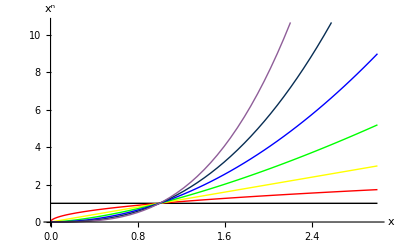

```mathematica
Plot[Table[x^n,{n,0,3,.5}],{x,0,3},PlotStyle->{Black,Red,Yellow,Green,Blue,Indigo,Violet},AxesLabel->{x,x^n},Evaluated->True]
```

## Sums

### ∑_(b=2)^∞ ∑_(a=2)^∞ 1/a^b==1

```mathematica
Sum[1/a^b,{b,2,∞},{a,2,∞}]
```

1

#### V7

```mathematica
Sum[1/a^b,{b,2,∞},{a,2,∞}]
```

1

### ∑_(n=0)^(N-1) p^n ⅇ^(ⅈ n x)==((ⅇ^(ⅈ x) p)^N-1)/(ⅇ^(ⅈ x) p-1)

```mathematica
Sum[p^n Exp[I n x],{n,0,N-1}]
```

(-1+(ⅇ^(ⅈ x) p)^N)/(-1+ⅇ^(ⅈ x) p)

#### V7

```mathematica
Sum[p^n Exp[I n x],{n,0,N-1}]
```

(-1+ⅇ^(ⅈ N x) p^N)/(-1+ⅇ^(ⅈ x) p)

```mathematica
FullSimplify[%]
```

(-1+ⅇ^(ⅈ N x) p^N)/(-1+ⅇ^(ⅈ x) p)

### ∑_(n=0)^∞ p^n ⅇ^(ⅈ n x)==(1-p ⅇ^(-ⅈ x))/(p^2-2 cos(x) p+1)

```mathematica
s=Sum[p^n Exp[I n x],{n,0,Infinity}]
```

-1/(-1+ⅇ^(ⅈ x) p)

```mathematica
Simplify[s-(1-p Exp[-I x])/(1-2 p Cos[x]+p^2)]
```

0

#### V7

```mathematica
Sum[p^n Exp[I n x],{n,0,Infinity}]
```

-1/(-1+ⅇ^(ⅈ x) p)

### ∑_k^n ∑_j^k (-1)^(k-j) j^n (k j) (x k)==x^n

```mathematica
Table[Sum[(-1)^(k-j)j^n Binomial[k,j]Binomial[x,k],{k,n},{j,k}],{n,10}]//FunctionExpand//Expand
```

{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

#### V6

```mathematica
Sum[(-1)^(k-j)j^n Binomial[k,j]Binomial[x,k],{k,n},{j,k}]
```

∑_k^n ∑_j^k (-1)^(-j+k) j^n Binomial[k,j] Binomial[x,k]

#### V7

```mathematica
Sum[(-1)^(k-j)j^n Binomial[k,j]Binomial[x,k],{k,n},{j,k}]
```

x^n

### (∑_k^(p+1) n^k -k+p+1 Binomial[p+1, k] (-1)^(k,p))/(p+1)==n-p

```mathematica
Sum[k^p,{k,n}]
```

HarmonicNumber[n,-p]

```mathematica
1/(p+1)Sum[(-1)^DiscreteDelta[k,p] Binomial[p+1,k]BernoulliB[p+1-k] n^k,{k,p+1}]
```

(∑_k^(1+p) (-1)^DiscreteDelta[k,p] n^k BernoulliB[1-k+p] Binomial[1+p,k])/(1+p)

```mathematica
1/(p+1)Sum[Binomial[p+1,k]BernoulliB[p+1-k] n^k,{k,p+1}]
```

(∑_k^(1+p) n^k BernoulliB[1-k+p] Binomial[1+p,k])/(1+p)

## Solutions of a^b==b^a

```mathematica
FullSimplify[Solve[a^b==b^a,a]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. More…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{a→-(b ProductLog[-Log[b]/b])/Log[b]}}

```mathematica
FullSimplify[Solve[a^b==b^a,b]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. More…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{b→-(a ProductLog[-Log[a]/a])/Log[a]}}

### b=2

```mathematica
FullSimplify[Solve[a^2==2^a,a]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. More…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{a→2},{a→-(2 ProductLog[Log[2]/2])/Log[2]},{a→4}}

```mathematica
N[%,10]
```

{{a→2.},{a→-0.766664696},{a→4.}}

### b=3

```mathematica
FullSimplify[Solve[a^3==3^a,a]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. More…

General::stop: Further output of InverseFunction :: "ifun" will be suppressed during this calculation. More…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{a→3},{a→-(3 ProductLog[-Log[3]/3])/Log[3]},{a→-(3 ProductLog[1/3 (-1)^(1/3) Log[3]])/Log[3]},{a→-(3 ProductLog[-1/3 (-1)^(2/3) Log[3]])/Log[3]}}

```mathematica
N[%]
```

{{a→3.},{a→2.47805},{a→-0.552925-0.60106 ⅈ},{a→-0.552925+0.60106 ⅈ}}

## Roots of -1

```mathematica
Show[GraphicsArray[
MapIndexed[Graphics[{Circle[{0,0},1],PointSize[.05],#1,Red,Point[Through[{Re,Im}[(-1)^(1/#2[[1]])]]]},AspectRatio->Automatic]&,Map[Point,
Map[{Re[#],Im[#]}&,Table[x/.{ToRules[Roots[x^n==-1,x]]},{n,5}],{2}],{2}]]]
]
```

⁃GraphicsArray⁃